## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP= λt*D[yt*P[xt, yt], xt]+D[yt*P[xt, yt], yt]-D[xt*P[xt, yt],yt]+(αt^2/2)D[P[xt, yt],{xt,2}]+(αtv^2/2)D[P[xt, yt],{yt,2}]/.{αt->0.01}
```

P[xt,yt]-xt P^(0,1)[xt,yt]+yt P^(0,1)[xt,yt]+1/2 αtv^2 P^(0,2)[xt,yt]+yt λt P^(1,0)[xt,yt]+0.00005 P^(2,0)[xt,yt]

## Get the steady-state variances

```mathematica
A= {{ 0,λt},{-1, 1}}
B = {{0.01,0},{0,αtv}}
s=Array[Y,{2,2}]
ss =( s/. Expand[FullSimplify[Solve[A.s+s.Transpose[A]==B.Transpose[B], Flatten[s]]]])[[1]]
```

{{0,λt},{-1,1}}

{{0.01,0},{0,αtv}}

{{Y[1,1],Y[1,2]},{Y[2,1],Y[2,2]}}

{{0.00005+0.00005/λt+0.5 αtv^2 λt,0.00005/λt},{0.00005/λt,0.5 αtv^2+0.00005/λt}}

```mathematica
Eigenvectors[A]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvectors[ss]
```

{{-1. (0.-0.5 λt+5000. αtv^2 λt-5000. αtv^2 λt^2+10000. √(1.×10^-8+2.5×10^-9 λt^2-0.00005 αtv^2 λt^2+0.25 αtv^4 λt^2+0.00005 αtv^2 λt^3-0.5 αtv^4 λt^3+0.25 αtv^4 λt^4)),1.},{-1. (0.-0.5 λt+5000. αtv^2 λt-5000. αtv^2 λt^2-10000. √(1.×10^-8+2.5×10^-9 λt^2-0.00005 αtv^2 λt^2+0.25 αtv^4 λt^2+0.00005 αtv^2 λt^3-0.5 αtv^4 λt^3+0.25 αtv^4 λt^4)),1.}}

```mathematica
Eigenvalues[ss]
```

{1/λt 0.5 (0.0001+0.00005 λt+0.5 αtv^2 λt+0.5 αtv^2 λt^2-√(1.×10^-8+2.5×10^-9 λt^2-0.00005 αtv^2 λt^2+0.25 αtv^4 λt^2+0.00005 αtv^2 λt^3-0.5 αtv^4 λt^3+0.25 αtv^4 λt^4)),1/λt 0.5 (0.0001+0.00005 λt+0.5 αtv^2 λt+0.5 αtv^2 λt^2+√(1.×10^-8+2.5×10^-9 λt^2-0.00005 αtv^2 λt^2+0.25 αtv^4 λt^2+0.00005 αtv^2 λt^3-0.5 αtv^4 λt^3+0.25 αtv^4 λt^4))}

## Choose the parameter values

```mathematica
λts = {0.005, 0.008, 0.01, 0.015, 0.02};
αtvs = {0.01, 0.02, 0.05, 0.075,0.1};
αArray2 = Flatten[Table[{αtvs },5]]^2
params = Flatten[Table[{λt->l, αtv->a}, {l, λts}, {a, αtvs}], 1]
legend =  Flatten[Table["λt="<>ToString[l]<>"; "<> "αtv="<>ToString[a], {l, λts},{a, αtvs}], 1];
```

{0.0001,0.0004,0.0025,0.005625,0.01,0.0001,0.0004,0.0025,0.005625,0.01,0.0001,0.0004,0.0025,0.005625,0.01,0.0001,0.0004,0.0025,0.005625,0.01,0.0001,0.0004,0.0025,0.005625,0.01}

{{λt→0.005,αtv→0.01},{λt→0.005,αtv→0.02},{λt→0.005,αtv→0.05},{λt→0.005,αtv→0.075},{λt→0.005,αtv→0.1},{λt→0.008,αtv→0.01},{λt→0.008,αtv→0.02},{λt→0.008,αtv→0.05},{λt→0.008,αtv→0.075},{λt→0.008,αtv→0.1},{λt→0.01,αtv→0.01},{λt→0.01,αtv→0.02},{λt→0.01,αtv→0.05},{λt→0.01,αtv→0.075},{λt→0.01,αtv→0.1},{λt→0.015,αtv→0.01},{λt→0.015,αtv→0.02},{λt→0.015,αtv→0.05},{λt→0.015,αtv→0.075},{λt→0.015,αtv→0.1},{λt→0.02,αtv→0.01},{λt→0.02,αtv→0.02},{λt→0.02,αtv→0.05},{λt→0.02,αtv→0.075},{λt→0.02,αtv→0.1}}

## Get the trajectory of the mean

```mathematica
eig=FullSimplify[Eigenvectors[A]]
```

{{1/2 (1+√(1-4 λt)),1},{1/2 (1-√(1-4 λt)),1}}

```mathematica
Eigenvalues[A]
```

{1/2 (1-√(1-4 λt)),1/2 (1+√(1-4 λt))}

```mathematica
cs =Re[N[ Flatten[Table[(eig[[1,1]])^-1/.p, {p, params}]]]]
```

{1.00505,1.00505,1.00505,1.00505,1.00505,1.00813,1.00813,1.00813,1.00813,1.00813,1.01021,1.01021,1.01021,1.01021,1.01021,1.01547,1.01547,1.01547,1.01547,1.01547,1.02084,1.02084,1.02084,1.02084,1.02084}

## Set up the mesh, boundary conditions, and initial condition

#### Steady-state distribution widths in x~, y~

```mathematica
xtwidths = N[Table[ss[[1,1]]/.p, {p, params}]];
ytwidths = N[Table[ss[[2,2]]/.p, {p, params}]];
xywidths =  N[Table[ss[[1,2]]/.p, {p, params}]];
xtStds =Sqrt[xtwidths]
ytStds = Sqrt[ytwidths]
covStds = Sqrt[xywidths]
```

{0.100251,0.100255,0.100281,0.10032,0.100374,0.0793751,0.0793826,0.0794355,0.0795141,0.0796241,0.0710669,0.0710774,0.0711512,0.071261,0.0714143,0.0581729,0.0581922,0.0583274,0.0585279,0.0588076,0.0505074,0.0505371,0.0507445,0.0510514,0.0514782}

{0.10025,0.100995,0.106066,0.113192,0.122474,0.0793725,0.0803119,0.0866025,0.0951972,0.106066,0.0710634,0.072111,0.0790569,0.0883883,0.1,0.0581664,0.0594418,0.0677003,0.0783954,0.0912871,0.0504975,0.0519615,0.0612372,0.0728869,0.0866025}

{0.1,0.1,0.1,0.1,0.1,0.0790569,0.0790569,0.0790569,0.0790569,0.0790569,0.0707107,0.0707107,0.0707107,0.0707107,0.0707107,0.057735,0.057735,0.057735,0.057735,0.057735,0.05,0.05,0.05,0.05,0.05}

```mathematica
θs = ArcTan[cs]
yt0 = 1+5*ytStds*Sin[θs]
xt0 = yt0/cs
```

{0.787917,0.787917,0.787917,0.787917,0.787917,0.789447,0.789447,0.789447,0.789447,0.789447,0.790475,0.790475,0.790475,0.790475,0.790475,0.793072,0.793072,0.793072,0.793072,0.793072,0.795712,0.795712,0.795712,0.795712,0.795712}

{1.35533,1.35797,1.37594,1.4012,1.4341,1.28176,1.28509,1.30742,1.33793,1.37652,1.25252,1.25624,1.28092,1.31408,1.35534,1.20722,1.21177,1.24119,1.27929,1.32522,1.18037,1.1856,1.21873,1.26034,1.30933}

{1.34852,1.35115,1.36903,1.39416,1.4269,1.27142,1.27473,1.29688,1.32714,1.36541,1.23987,1.24355,1.26798,1.30081,1.34165,1.18883,1.19331,1.22228,1.2598,1.30503,1.15627,1.16139,1.19385,1.23461,1.2826}

```mathematica
Δx = 5*Sqrt[αArray2]/Cos[(Pi/2)-θs]
Δy =5*Sqrt[Table[Max[ss[[1,2]]/.p,ss[[2,2]]/.p ],{p,params}]]*Sin[θs]
lrange =ArrayReshape[ Transpose[Table[λts,5]], {1, 25}][[1]]
ΩFunc[Δx_, Δy_, λ_, xt0_, yt0_] :=Parallelogram[{1/2 (1+√(1-4 λ))-Δx, 1}, {{2Δx, 0}, {(yt0-1+Δy)*(1/2 (1+√(1-4 λ))),(yt0-1+Δy)}}]
Ω=MapThread[ΩFunc,{Δx, Δy, lrange,xt0,yt0}];
```

{0.0705332,0.141066,0.352666,0.528999,0.705332,0.0704261,0.140852,0.352131,0.528196,0.704261,0.0703544,0.140709,0.351772,0.527658,0.703544,0.0701742,0.140348,0.350871,0.526307,0.701742,0.0699926,0.139985,0.349963,0.524944,0.699926}

{0.355328,0.35797,0.375943,0.401202,0.434102,0.281758,0.285093,0.307423,0.337933,0.376515,0.252519,0.256242,0.280924,0.314082,0.355344,0.207222,0.211765,0.241187,0.279288,0.325216,0.180367,0.185597,0.218728,0.260338,0.309328}

{0.005,0.005,0.005,0.005,0.005,0.008,0.008,0.008,0.008,0.008,0.01,0.01,0.01,0.01,0.01,0.015,0.015,0.015,0.015,0.015,0.02,0.02,0.02,0.02,0.02}

```mathematica
Ω[[1]]
```

Parallelogram[{0.924442,1},{{0.141066,0},{0.707084,0.710656}}]

```mathematica
Sqrt[αtvs[[1]]^2]
maxCell = Sqrt[αArray2]/8
```

0.01

{0.00125,0.0025,0.00625,0.009375,0.0125,0.00125,0.0025,0.00625,0.009375,0.0125,0.00125,0.0025,0.00625,0.009375,0.0125,0.00125,0.0025,0.00625,0.009375,0.0125,0.00125,0.0025,0.00625,0.009375,0.0125}

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
meshes = MapThread[ToElementMesh[#1, MaxCellMeasure->{"Length"->#2}, MaxBoundaryCellMeasure->{"Length"->#2}]&, {Ω, maxCell}]
```

{ElementMesh[{{0.924442,1.77259},{1.,1.71066}},{TriangleElement[<468678>]}],ElementMesh[{{0.853908,1.84838},{1.,1.71594}},{TriangleElement[<236189>]}],ElementMesh[{{0.642309,2.09575},{1.,1.75189}},{TriangleElement[<99206>]}],ElementMesh[{{0.465976,2.32235},{1.,1.8024}},{TriangleElement[<70229>]}],ElementMesh[{{0.289642,2.56415},{1.,1.8682}},{TriangleElement[<57207>]}],ElementMesh[{{0.921509,1.62133},{1.,1.56352}},{TriangleElement[<371538>]}],ElementMesh[{{0.851083,1.69837},{1.,1.57019}},{TriangleElement[<187829>]}],ElementMesh[{{0.639804,1.95395},{1.,1.61485}},{TriangleElement[<80814>]}],ElementMesh[{{0.463739,2.19055},{1.,1.67587}},{TriangleElement[<59236>]}],ElementMesh[{{0.287674,2.44315},{1.,1.75303}},{TriangleElement[<49634>]}],ElementMesh[{{0.919544,1.56019},{1.,1.50504}},{TriangleElement[<332002>]}],ElementMesh[{{0.849189,1.63791},{1.,1.51248}},{TriangleElement[<168553>]}],ElementMesh[{{0.638126,1.89784},{1.,1.56185}},{TriangleElement[<73900>]}],ElementMesh[{{0.46224,2.13938},{1.,1.62816}},{TriangleElement[<54917>]}],ElementMesh[{{0.286354,2.39695},{1.,1.71069}},{TriangleElement[<46856>]}],ElementMesh[{{0.914594,1.46307},{1.,1.41444}},{TriangleElement[<272140>]}],ElementMesh[{{0.84442,1.5422},{1.,1.42353}},{TriangleElement[<138692>]}],ElementMesh[{{0.633897,1.81066},{1.,1.48237}},{TriangleElement[<63093>]}],ElementMesh[{{0.458461,2.06114},{1.,1.55858}},{TriangleElement[<48640>]}],ElementMesh[{{0.283026,2.32703},{1.,1.65043}},{TriangleElement[<42804>]}],ElementMesh[{{0.909591,1.40295},{1.,1.36073}},{TriangleElement[<236053>]}],ElementMesh[{{0.839598,1.48318},{1.,1.37119}},{TriangleElement[<121390>]}],ElementMesh[{{0.62962,1.75807},{1.,1.43746}},{TriangleElement[<57345>]}],ElementMesh[{{0.454639,2.01457},{1.,1.52068}},{TriangleElement[<45439>]}],ElementMesh[{{0.279658,2.28553},{1.,1.61866}},{TriangleElement[<40560>]}]}

```mathematica
meshes[[25]]["Wireframe"]
```

-Graphics-

```mathematica
bcs=Table[DirichletCondition[P[xt,yt]==0,ElementMarker==#]&/@m["BoundaryElementMarkerUnion"], {m, meshes}];
```

```mathematica
icPos =Transpose[{xt0, yt0}]
icVar =Table[ss/.p, {p, params}]
ic0 = N[MapThread[PDF[MultinormalDistribution[#1,#2], {xt, yt}]&, {icPos, icVar}]]
```

{{1.34852,1.35533},{1.35115,1.35797},{1.36903,1.37594},{1.39416,1.4012},{1.4269,1.4341},{1.27142,1.28176},{1.27473,1.28509},{1.29688,1.30742},{1.32714,1.33793},{1.36541,1.37652},{1.23987,1.25252},{1.24355,1.25624},{1.26798,1.28092},{1.30081,1.31408},{1.34165,1.35534},{1.18883,1.20722},{1.19331,1.21177},{1.22228,1.24119},{1.2598,1.27929},{1.30503,1.32522},{1.15627,1.18037},{1.16139,1.1856},{1.19385,1.21873},{1.23461,1.26034},{1.2826,1.30933}}

{{{0.0100503,0.01},{0.01,0.01005}},{{0.010051,0.01},{0.01,0.0102}},{{0.0100563,0.01},{0.01,0.01125}},{{0.0100641,0.01},{0.01,0.0128125}},{{0.010075,0.01},{0.01,0.015}},{{0.0063004,0.00625},{0.00625,0.0063}},{{0.0063016,0.00625},{0.00625,0.00645}},{{0.00631,0.00625},{0.00625,0.0075}},{{0.0063225,0.00625},{0.00625,0.0090625}},{{0.00634,0.00625},{0.00625,0.01125}},{{0.0050505,0.005},{0.005,0.00505}},{{0.005052,0.005},{0.005,0.0052}},{{0.0050625,0.005},{0.005,0.00625}},{{0.00507813,0.005},{0.005,0.0078125}},{{0.0051,0.005},{0.005,0.01}},{{0.00338408,0.00333333},{0.00333333,0.00338333}},{{0.00338633,0.00333333},{0.00333333,0.00353333}},{{0.00340208,0.00333333},{0.00333333,0.00458333}},{{0.00342552,0.00333333},{0.00333333,0.00614583}},{{0.00345833,0.00333333},{0.00333333,0.00833333}},{{0.002551,0.0025},{0.0025,0.00255}},{{0.002554,0.0025},{0.0025,0.0027}},{{0.002575,0.0025},{0.0025,0.00375}},{{0.00260625,0.0025},{0.0025,0.0053125}},{{0.00265,0.0025},{0.0025,0.0075}}}

{158.758 2.71828^(0.5 (-1. (-1.34852+xt) (9999.88 (-1.34852+xt)-9950.12 (-1.35533+yt))-1. (-9950.12 (-1.34852+xt)+10000.1 (-1.35533+yt)) (-1.35533+yt))),100.254 2.71828^(0.5 (-1. (-1.35115+xt) (4047.3 (-1.35115+xt)-3967.94 (-1.35797+yt))-1. (-3967.94 (-1.35115+xt)+3988.18 (-1.35797+yt)) (-1.35797+yt))),43.9179 2.71828^(0.5 (-1. (-1.36903+xt) (856.633 (-1.36903+xt)-761.452 (-1.37594+yt))-1. (-761.452 (-1.36903+xt)+765.735 (-1.37594+yt)) (-1.37594+yt))),29.582 2.71828^(0.5 (-1. (-1.39416+xt) (442.638 (-1.39416+xt)-345.473 (-1.4012+yt))-1. (-345.473 (-1.39416+xt)+347.686 (-1.4012+yt)) (-1.4012+yt))),22.2589 2.71828^(0.5 (-1. (-1.4269+xt) (293.399 (-1.4269+xt)-195.599 (-1.4341+yt))-1. (-195.599 (-1.4269+xt)+197.066 (-1.4341+yt)) (-1.4341+yt))),200.513 2.71828^(0.5 (-1. (-1.27142+xt) (9999.68 (-1.27142+xt)-9920.32 (-1.28176+yt))-1. (-9920.32 (-1.27142+xt)+10000.3 (-1.28176+yt)) (-1.28176+yt))),126.504 2.71828^(0.5 (-1. (-1.27473+xt) (4075.01 (-1.27473+xt)-3948.65 (-1.28509+yt))-1. (-3948.65 (-1.27473+xt)+3981.25 (-1.28509+yt)) (-1.28509+yt))),55.3687 2.71828^(0.5 (-1. (-1.29688+xt) (907.716 (-1.29688+xt)-756.43 (-1.30742+yt))-1. (-756.43 (-1.29688+xt)+763.691 (-1.30742+yt)) (-1.30742+yt))),37.2705 2.71828^(0.5 (-1. (-1.32714+xt) (496.98 (-1.32714+xt)-342.745 (-1.33793+yt))-1. (-342.745 (-1.32714+xt)+346.72 (-1.33793+yt)) (-1.33793+yt))),28.0202 2.71828^(0.5 (-1. (-1.36541+xt) (348.702 (-1.36541+xt)-193.723 (-1.37652+yt))-1. (-193.723 (-1.36541+xt)+196.513 (-1.37652+yt)) (-1.37652+yt))),223.957 2.71828^(0.5 (-1. (-1.23987+xt) (9999.5 (-1.23987+xt)-9900.5 (-1.25252+yt))-1. (-9900.5 (-1.23987+xt)+10000.5 (-1.25252+yt)) (-1.25252+yt))),141.205 2.71828^(0.5 (-1. (-1.24355+xt) (4093.2 (-1.24355+xt)-3935.77 (-1.25624+yt))-1. (-3935.77 (-1.24355+xt)+3976.7 (-1.25624+yt)) (-1.25624+yt))),61.7612 2.71828^(0.5 (-1. (-1.26798+xt) (941.176 (-1.26798+xt)-752.941 (-1.28092+yt))-1. (-752.941 (-1.26798+xt)+762.353 (-1.28092+yt)) (-1.28092+yt))),41.5492 2.71828^(0.5 (-1. (-1.30081+xt) (532.446 (-1.30081+xt)-340.765 (-1.31408+yt))-1. (-340.765 (-1.30081+xt)+346.09 (-1.31408+yt)) (-1.31408+yt))),31.2129 2.71828^(0.5 (-1. (-1.34165+xt) (384.615 (-1.34165+xt)-192.308 (-1.35534+yt))-1. (-192.308 (-1.34165+xt)+196.154 (-1.35534+yt)) (-1.35534+yt))),273.605 2.71828^(0.5 (-1. (-1.18883+xt) (9998.89 (-1.18883+xt)-9851.12 (-1.20722+yt))-1. (-9851.12 (-1.18883+xt)+10001.1 (-1.20722+yt)) (-1.20722+yt))),172.23 2.71828^(0.5 (-1. (-1.19331+xt) (4137.72 (-1.19331+xt)-3903.51 (-1.21177+yt))-1. (-3903.51 (-1.19331+xt)+3965.57 (-1.21177+yt)) (-1.21177+yt))),75.1788 2.71828^(0.5 (-1. (-1.22228+xt) (1022.66 (-1.22228+xt)-743.754 (-1.24119+yt))-1. (-743.754 (-1.22228+xt)+759.094 (-1.24119+yt)) (-1.24119+yt))),50.4769 2.71828^(0.5 (-1. (-1.2598+xt) (618.196 (-1.2598+xt)-335.292 (-1.27929+yt))-1. (-335.292 (-1.2598+xt)+344.565 (-1.27929+yt)) (-1.27929+yt))),37.8209 2.71828^(0.5 (-1. (-1.30503+xt) (470.588 (-1.30503+xt)-188.235 (-1.32522+yt))-1. (-188.235 (-1.30503+xt)+195.294 (-1.32522+yt)) (-1.32522+yt))),315.143 2.71828^(0.5 (-1. (-1.15627+xt) (9998.04 (-1.15627+xt)-9802. (-1.18037+yt))-1. (-9802. (-1.15627+xt)+10002. (-1.18037+yt)) (-1.18037+yt))),198.048 2.71828^(0.5 (-1. (-1.16139+xt) (4180.86 (-1.16139+xt)-3871.17 (-1.1856+yt))-1. (-3871.17 (-1.16139+xt)+3954.78 (-1.1856+yt)) (-1.1856+yt))),86.2347 2.71828^(0.5 (-1. (-1.19385+xt) (1100.92 (-1.19385+xt)-733.945 (-1.21873+yt))-1. (-733.945 (-1.19385+xt)+755.963 (-1.21873+yt)) (-1.21873+yt))),57.7479 2.71828^(0.5 (-1. (-1.23461+xt) (699.409 (-1.23461+xt)-329.133 (-1.26034+yt))-1. (-329.133 (-1.23461+xt)+343.122 (-1.26034+yt)) (-1.26034+yt))),43.1173 2.71828^(0.5 (-1. (-1.2826+xt) (550.459 (-1.2826+xt)-183.486 (-1.30933+yt))-1. (-183.486 (-1.2826+xt)+194.495 (-1.30933+yt)) (-1.30933+yt)))}

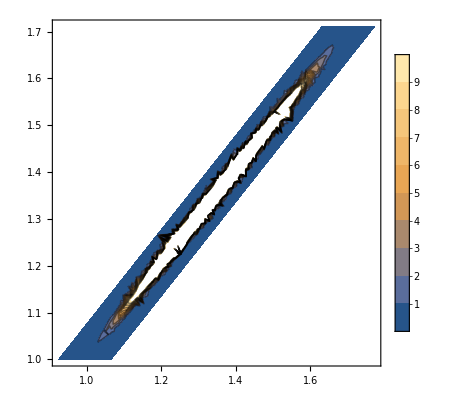

```mathematica
toPlot=1;
ContourPlot[ic0[[toPlot]], {xt,yt}∈Ω[[toPlot]], PlotRange->{0,10}, PlotLegends->Automatic, PerformanceGoal->"Quality"]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{xt, yt}∈reg, 
Method->{"FiniteElement"}] ;
Print["test"];
Return[(P/.N[[1]])];
]
```

```mathematica
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, meshes}];
```

test

test

test

«22 more identical outputs»

```mathematica
dv = Table[Derivative[0,1][sol], {sol, solsIc0}];
```

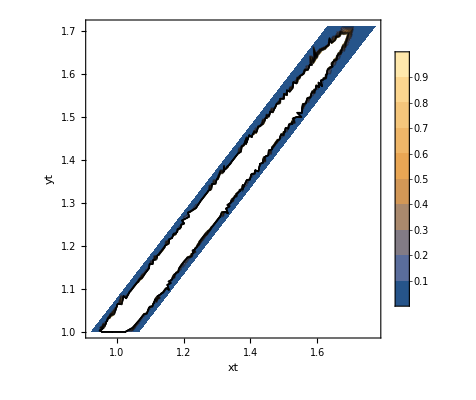

```mathematica
toPlot=1;
ContourPlot[solsIc0[[toPlot]][xt, yt], {xt,yt}∈Ω[[toPlot]], AxesLabel->{xt, yt}, PlotRange->{0, 1}, PlotLegends->Automatic, PerformanceGoal->"Quality"]
```

```mathematica
XIc0 =(MapThread[#1[xt,#2]&,{dv,Table[1, 25]}])*(αArray2/2);
bounds = Transpose[{1/cs-Δx/2, 1/cs+Δx/2}];
```

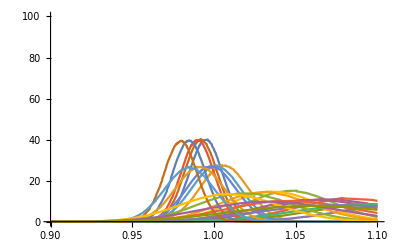

```mathematica
Plot[XIc0, {xt,0.9, 1.4}, PlotLegends->legend[[1]], PlotRange->{-0.1, 100}]
```

```mathematica
IntegFunc[f_, bound_] :=NIntegrate[f, {xt, bound[[1]], bound[[2]]}]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0,bounds}]
corrected = MapThread[#1/#2&, {XIc0, normsIc0}];
meansIc0= MapThread[IntegFunc, {corrected*xt,bounds}]
secondIc0 = MapThread[IntegFunc, {corrected*xt*xt,bounds}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0^2;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.995662}. NIntegrate obtained 0.998722 and 0.000041666 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00269}. NIntegrate obtained 0.999859 and 0.0000476356 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.09209}. NIntegrate obtained 0.998825 and 0.0000740125 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.998722,0.999859,0.998825,0.997257,0.99573,0.998207,1.00012,0.999101,0.997923,0.997206,0.997671,1.00008,0.999421,0.998461,0.996993,0.996025,0.999594,0.999613,0.998913,0.998082,0.994763,0.99931,1.00002,0.999474,0.998536}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.994423}. NIntegrate obtained 0.994909 and 0.0000314553 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00269}. NIntegrate obtained 1.00618 and 0.0000481236 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.09209}. NIntegrate obtained 1.04806 and 0.0000848183 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.994909,1.00618,1.04806,1.0871,1.12802,0.991881,1.00132,1.03807,1.07313,1.11028,0.989845,0.998349,1.03245,1.06549,1.10069,0.984716,0.99142,1.0205,1.04967,1.08121,0.979528,0.985015,1.01036,1.03661,1.06538}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {0.994423}. NIntegrate obtained 0.989971 and 0.0000309312 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.00269}. NIntegrate obtained 1.0126 and 0.0000472414 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in xt near {xt} = {1.09209}. NIntegrate obtained 1.09913 and 0.0000904922 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.989971,1.0126,1.09913,1.18307,1.27442,0.983932,1.00285,1.07834,1.15301,1.23487,0.979893,0.996897,1.06674,1.13672,1.21375,0.969765,0.983218,1.04225,1.10338,1.1715,0.959574,0.970469,1.02173,1.07627,1.13771}

{0.000126377,0.00020641,0.000712947,0.00129028,0.00198143,0.000104173,0.000216464,0.000755786,0.00139869,0.00214164,0.000100441,0.000195981,0.000782427,0.00143949,0.00223273,0.0000995515,0.000303936,0.000833164,0.00158319,0.00249194,0.0000984392,0.000215541,0.000896725,0.00169814,0.00268515}

```mathematica
grid = Flatten[Table[{l, a}, {l, λts}, {a, αtvs}], 1];
params
```

{{λt→0.005,αtv→0.01},{λt→0.005,αtv→0.02},{λt→0.005,αtv→0.05},{λt→0.005,αtv→0.075},{λt→0.005,αtv→0.1},{λt→0.008,αtv→0.01},{λt→0.008,αtv→0.02},{λt→0.008,αtv→0.05},{λt→0.008,αtv→0.075},{λt→0.008,αtv→0.1},{λt→0.01,αtv→0.01},{λt→0.01,αtv→0.02},{λt→0.01,αtv→0.05},{λt→0.01,αtv→0.075},{λt→0.01,αtv→0.1},{λt→0.015,αtv→0.01},{λt→0.015,αtv→0.02},{λt→0.015,αtv→0.05},{λt→0.015,αtv→0.075},{λt→0.015,αtv→0.1},{λt→0.02,αtv→0.01},{λt→0.02,αtv→0.02},{λt→0.02,αtv→0.05},{λt→0.02,αtv→0.075},{λt→0.02,αtv→0.1}}

```mathematica
normArrayIc0 = ArrayReshape[normsIc0, {5,5}];
varArrayIc0 = ArrayReshape[varsIc0, {5,5}];
meanArrayIc0 = ArrayReshape[meansIc0, {5,5}];
diffArrayIc0 = ArrayReshape[diffIc0,{5,5}];
```

```mathematica
cf[x_]:=Blend[{{0, Red},{ 1,White},{2,Blue}}, x]
xticks = Transpose[{{1, 2, 3, 4, 5}, λts}];
yticks = Transpose[{{1, 2, 3, 4, 5}, αtvs}];
```

```mathematica
ArrayPlot[Sqrt[varArrayIc0], ColorFunction->(Blend[{{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"Var("OverTilde[xt]   .")"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[Sqrt[varArrayIc0]],5]]
Grid[N[Reverse[normArrayIc0],5]]
```

0.00992165 | 0.0146813 | 0.0299454 | 0.0412085 | 0.0518184
0.00997755 | 0.0174338 | 0.0288646 | 0.0397894 | 0.0499194
0.010022 | 0.0139993 | 0.0279719 | 0.0379407 | 0.0472518
0.0102065 | 0.0147127 | 0.0274916 | 0.0373991 | 0.0462779
0.0112417 | 0.014367 | 0.0267011 | 0.0359205 | 0.0445133

0.994763 | 0.99931 | 1.00002 | 0.999474 | 0.998536
0.996025 | 0.999594 | 0.999613 | 0.998913 | 0.998082
0.997671 | 1.00008 | 0.999421 | 0.998461 | 0.996993
0.998207 | 1.00012 | 0.999101 | 0.997923 | 0.997206
0.998722 | 0.999859 | 0.998825 | 0.997257 | 0.99573

```mathematica
ArrayPlot[ArrayReshape[Table[Blend[{{0, Red},{ 1,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {5,5}], PlotLegends->{Placed[BarLegend[{cf[#]&,{0, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, αt}]
Grid[N[Reverse[meanArrayIc0],5]]
```

-Graphics-

0.979528 | 0.985015 | 1.01036 | 1.03661 | 1.06538
0.984716 | 0.99142 | 1.0205 | 1.04967 | 1.08121
0.989845 | 0.998349 | 1.03245 | 1.06549 | 1.10069
0.991881 | 1.00132 | 1.03807 | 1.07313 | 1.11028
0.994909 | 1.00618 | 1.04806 | 1.0871 | 1.12802

```mathematica
Grid[1/Reverse[ArrayReshape[cs, {5, 5}]]]
```

0.723607 | 0.723607 | 0.723607 | 0.723607 | 0.723607
0.816228 | 0.816228 | 0.816228 | 0.816228 | 0.816228
0.887298 | 0.887298 | 0.887298 | 0.887298 | 0.887298
0.912311 | 0.912311 | 0.912311 | 0.912311 | 0.912311
0.947214 | 0.947214 | 0.947214 | 0.947214 | 0.947214

```mathematica
Table[(1+Sqrt[1-4l])/2, {l, {0.05, 0.08, 0.1, 0.15,0.2}}]
```

{0.947214,0.912311,0.887298,0.816228,0.723607}

```mathematica
f1 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, %210}]]
```

InterpolatingFunction[…]

```mathematica
f2 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.09,1.01, 0.97,0.86,0.74 }-%210}]]
```

InterpolatingFunction[…]

```mathematica
f3 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.09, 1.01, 0.97, 0.86, 0.74}}]]
```

InterpolatingFunction[…]

```mathematica
f4 = Interpolation[Transpose[{{0.05, 0.08, 0.1, 0.15,0.2}, {1.04, 0.98, 0.94, 0.84, 0.73}}]]
```

InterpolatingFunction[…]

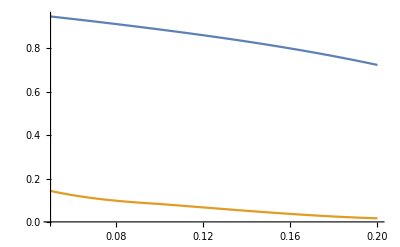

```mathematica
Plot[{f1[x], f2[x]}, {x, 0.05, 0.2}]
```

```mathematica
ArrayPlot[diffArrayIc0, ColorFunction->(Blend[{{ 0,White},{3,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"varScaledToMean2(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λt, κt}]
Grid[N[Reverse[diffArrayIc0],4]]
```

-Graphics-

-0.000953224 | 0.00319174 | 0.012927 | 0.0530549 | 0.123451
0.000445732 | 0.0027794 | 0.0112394 | 0.0456622 | 0.104291
0.000416853 | 0.00262419 | 0.0104487 | 0.0420214 | 0.0967817
0.000416854 | 0.00254727 | 0.0103964 | 0.0406542 | 0.0924427
0.000396373 | 0.00254852 | 0.0100826 | 0.0404404 | 0.0913144